```mathematica
(*PARAMETERS OF THE HAMILTONIAN*)
AbsoluteTiming[
x=AbsoluteTime[];
Clear[L,upspins,downspins,dim,Jxy,Jz,Ε,defectsite,alpha,JJxy,JJz];
L=18;
upspins=L/3;
downspins=L-upspins;
dim=L! /(upspins! downspins!);
dim
(*Impurity*)
ϵ=0;
defectsite=Floor[L/2];
(*Parameters for nearest-neighbor couplings*)
Jxy=1;
Jz=0.5;
(*Parameters for next-nearest-neighbor couplings*)
(*Set alpha=0 if NNN couplings do not exist*)
alpha=0.8;
JJxy=1;
JJz=0;
(*BASIS*)
Clear[onebasisvector,basis];
onebasisvector=Flatten[{Table[1,{k,1,upspins}],Table[0,{k,1,downspins}]}];
basis=Permutations[onebasisvector];
]
basis
```

{0.0009919,Null}

```mathematica
AbsoluteTiming[
(*elements of the Hamiltonian*)
(*Impurities and NN*)
Clear[HH];
Do[Do[HH[i,j]=0,{i,1,dim}],{j,1,dim}];

(*Diagonals*)

Associatedvectors=ConstantArray[{},dim];
Associatedvectors2=ConstantArray[{},dim];
(*in an index, will be all of the vectors before that index that mapped to the index at that vector*)

Do[
(*Impurity*)
(*If[basis[[i,defectsite]]==1,HH[i,i]=HH[i,i]+ϵ/2,HH[i,i]=HH[i,i]-ϵ/2];*)
(*Ising interaction*)
Do[
(*NN*)

(*Diag*)
If[basis[[i,j]]==basis[[i,j+1]],HH[i,i]=HH[i,i]+Jz/4,HH[i,i]=HH[i,i]-Jz/4];

tempbasisv={2};

(*Off Diag*)
	If[basis[[i,j]]==1 && basis[[i,j+1]]==0,tempbasisv=ReplacePart[ReplacePart[basis[[i]],j-> 0],j+1-> 1]];

If[basis[[i,j]]==0 && basis[[i,j+1]]==1,tempbasisv=ReplacePart[ReplacePart[basis[[i]],j-> 1],j+1-> 0]];

If[tempbasisv[[1]]≠2 && !(MemberQ[Associatedvectors[[i]],tempbasisv]),Do[If[tempbasisv==basis[[k]],{HH[i,k]=Jxy/2,HH[k,i]=Jxy/2,Associatedvectors[[k]]=Append[Associatedvectors[[k]],basis[[i]]],Break[]}],{k,i+1,dim}]];

(*NNN*)


(*Diag*)
If[basis[[i,j]]==basis[[i,j+2]],HH[i,i]=HH[i,i]+alpha JJz/4,HH[i,i]=HH[i,i]-alpha JJz/4];
(*Off Diag*)

tempbasisv2={2};

If[basis[[i,j]]==1 && basis[[i,j+2]]==0,tempbasisv2=ReplacePart[ReplacePart[basis[[i]],j-> 0],j+2-> 1]];

If[basis[[i,j]]==0 && basis[[i,j+2]]==1,tempbasisv2=ReplacePart[ReplacePart[basis[[i]],j-> 1],j+2-> 0]];

If[tempbasisv2[[1]]≠2 && !(MemberQ[Associatedvectors2[[i]],tempbasisv]), Do[If[tempbasisv2==basis[[k]],{HH[i,k]=alpha JJxy/2 , HH[k,i]=alpha JJxy/2,Associatedvectors2[[k]]=Append[Associatedvectors2[[k]],basis[[i]]],Break[]}],{k,i+1,dim}]];

,{j,1,L-2}];

If[basis[[i,L-1]]==basis[[i,L]],HH[i,i]=HH[i,i]+Jz/4,HH[i,i]=HH[i,i]-Jz/4];

tempbasisv={2};

(*Off Diag*)
	If[basis[[i,L-1]]==1 && basis[[i,L]]==0,tempbasisv=ReplacePart[ReplacePart[basis[[i]],L-1-> 0],L-> 1]];

If[basis[[i,L-1]]==0 && basis[[i,L]]==1,tempbasisv=ReplacePart[ReplacePart[basis[[i]],L-1-> 1],L-> 0]];

If[tempbasisv[[1]]≠2,Do[If[tempbasisv==basis[[k]],{HH[i,k]=Jxy/2,HH[k,i]=Jxy/2,Break[]}],{k,i+1,dim}]]; (*HERE*)

,{i,1,dim}]
]
(*New method to optimise, for the line of type HERE, even if tempbasisv near the beginning is paired with one a few basis later, when we *)
(*Each basis vector that has been paired to gets associated with it the baisis vector that paired to it, then wheen you reach a basis vector, you first check the list of basis vectors that have already paired to it, and break the loop in HERE if tempbasisv is in the list (having the limits be from k to i+1already tries to do decrease number of if checks by average of 2. with L/3 up, have 2L possible ways of getting a swap, thus the list associated with each basisv is probably around 2L/2 =L, the other L are to be checked brute force as usual, brute force -> average of dim/2 checks, thus expected value is 0.5 L + 0.5 dim/2 vs dim/2, and since L<<dim, this is about 0.5 dim)*)

(*New method to optimise, for using multiple values of α, between α's, the only thing that changes is the NNN interactions, so can use old HH matrix, only multiplying the NNN values by alpha_new/alpha_old*)
(*77.15 without second break*)
(*58.25 with break*)
```

{887.215,Null}

```mathematica
AbsoluteTiming[
(*Total H and diagonalisation*)
Clear[Hamiltonian,Energy,Vector];
Hamiltonian=Table[Table[HH[i,j],{i,1,dim}],{j,1,dim}];
{Energy,Vector}=Eigensystem[Hamiltonian];
(*15min 3 seconds*)
(*Energy=Eigenvalues[Hamiltonian];
Vector=Eigenvectors[Hamiltonian];*)
(*14min 43 seconds, a=0.8*)
(**)
]
(*13.4 list assign*)
(*16.8 the other way*)
```

{870.66,Null}

```mathematica
Energy;
```

```mathematica
(*{3.53877161643474,3.0045668049713847,2.5230286030667144,2.4605377004962095,2.2636390679581875,-2.1855442974642743,-2.1430256312872755,-2.0666699977003584,-2.044159451974404,2.0344001386047563,-2.0061897072214654,1.9479479451543367,-1.9349331567797898,-1.909638503511438,1.8263048930401191,-1.770962708823122,-1.6734503282285749,1.6381384054840997,1.6320873545209205,-1.6300762944486547,1.552268102857957,-1.4910436588509848,1.4567957236185083,-1.4413932073214157,1.4389189788553995,-1.408784684551176,-1.3642252450888217,1.3178886113638217,1.2879106398917077,1.2408482862790016,-1.2332087688551803,-1.1668790995928149,1.1518768294021418,-1.1374467082493114,1.1187816358141425,-1.094202258637613,-1.0739981020367806,-1.0139273741828676,1.0090429348713115,1.0017236886483736,-0.9922312297546172,-0.9681777848325732,0.9246187011357505,-0.9131843655884284,0.884663617827897,-0.8537985442090987,0.8322087827332547,-0.8299366886777382,-0.7980025104850086,0.7391967278779163,0.7275977177598842,-0.6800136165829187,-0.6757056910151356,0.663854454386184,-0.6268511572181219,-0.6142631721194487,0.5792856531928465,-0.5681267828737542,-0.5562026790844878,-0.5369872914675624,0.5247208662155431,0.4661769225653467,0.4583130371487574,-0.421788569874739,-0.37440690446701796,0.361328551867123,-0.339685288830081,-0.33613648281794983,0.3241500483485824,-0.31324281097958284,-0.26601999541737475,0.2625718765021259,-0.20379947320970881,0.20290976969807817,0.18740116742160007,0.1842279112635694,-0.1668662551837139,-0.1242155043164086,0.09517867766972987,0.06890545926923064,0.03848694790833784,-0.03838982597109153,0.022954562319852823,-0.006437604662599572}*)
```

```mathematica
Reversedbasis=Map[Reverse,basis];
Findpair[i_]:=Module[{paired},
Do[If[basis[[i]]==Reversedbasis[[j]],{paired=j,Break[]}],{j,1,dim}];
Return[paired]
]
```

```mathematica
Findpair[7]
```

18102

```mathematica
AbsoluteTiming[

(*Reversedbasis=Map[Reverse,basis];
pair=ConstantArray[0,dim];
paired=0;
Do[
If[basis[[3]]==Reversedbasis[[j]],{paired=j,Break[]}]
,{j,1,dim}]*)

(*ATTEMPT 2*)
Neven=0;
Nodd=0;
Pairs=ConstantArray[0,dim];
Pairedindex={};
Do[
Do[
If[Abs[Vector[[j]][[i]]]≥1/(√(20 dim)) &&  MemberQ[Pairedindex,i],{If[(Vector[[j]][[i]]≥0 && Vector[[j]][[Pairs[[i]]]] ≥ 0) || (Vector[[j]][[i]]≤ 0 && Vector[[j]][[Pairs[[i]]]] ≤  0),{Neven+=1,even[Neven]=j},{Nodd+=1,odd[Nodd]=j}],Break[]}];
If[Abs[Vector[[j]][[i]]]≥1/(√(20 dim)) ,{Pairs[[i]]=Findpair[i],Pairedindex=Append[Pairedindex,i],{If[(Vector[[j]][[i]]≥0 && Vector[[j]][[Pairs[[i]]]] ≥ 0) || (Vector[[j]][[i]]≤ 0 && Vector[[j]][[Pairs[[i]]]] ≤  0),{Neven+=1,even[Neven]=j},{Nodd+=1,odd[Nodd]=j}],Break[]}}]
,{i,1,Ceiling[dim/2]}]
,{j,1,dim}]
]

(*Can cheat more here by only checking one basis vector lol*)
(*Use cheat code! each vector is either positive or negative under parity transformation, so each component will go to either plus itself or minus itself, so only need to check one component and note if there is a sign change*)
(*Need a function which takes the eigenvators, and returns a list where the eigenenergies are associated with eigenvectors with even parity*)
(*Clear[i,j,k,pair];
Do[
Do[
Clear[mirror];
mirror=0;
Do[mirror=mirror+Mod[basis[[i,k]]+basis[[j,L+1-k]],2],
{k,1,L}];
If[mirror==0,pair[i]=j],
{j,1,dim}],
{i,1,dim}];*)
```

{11.6357,Null}

```mathematica
(*Level spacing distribution 3for NN and NNN (parity is taken into account)*)
(*Parity*)
(*First we find all pairs of equivalent basis vectors*)
(*Example: state 1100 pairs with 0011*)
(*AbsoluteTiming[
(*Now we seperate eigenstates according to their parity*)
Clear[Neven,Nodd];
Neven=0;
Nodd=0;
Do[
Clear[project];
project=0;
Do[project=project+(1/4)(Vector[[i]][[j]]+Vector[[i]][[pair[j]]])^2,
{j,1,dim}];
(*project close to 1 even, 0 odd*)
If[1-project<0.001,{Neven=Neven+1,even[Neven]=i},{Nodd=Nodd+1,odd[Nodd]=i}],
{i,1,dim}]
Neven;
]*)
```

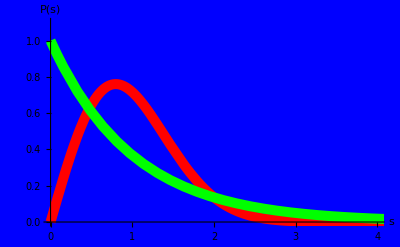

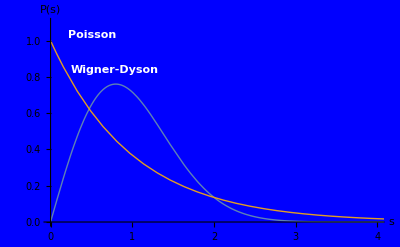

```mathematica
(*For the histogram (?)*)
Clear[spcmin,spcmax,bin,Nofbins];
spcmin=0;
spcmax=8;
bin=0.05;
Nofbins=IntegerPart[(spcmax-spcmin)/bin];
(*Theory curves*)
Clear[WignerDyson,Poisson];
WignerDyson=
Plot[Pi s/2.Exp[-Pi s^2/4.],{s,0,8},PlotRange->{0,1},PlotStyle->{Red,Thickness[0.018]},LabelStyle-> Directive[White,Bold,Medium],AxesLabel-> {"s","P(s)"}];
Poisson=Plot[Exp[-s],{s,0,8},PlotRange-> {0,1},PlotStyle-> {Green,Thickness[0.018]},LabelStyle-> Directive[White,Bold,Medium],AxesLabel-> {"s","P(s)"},PlotLabel->{"Poisson"}];

Show[{WignerDyson,Poisson},PlotRange-> {{0,4},{0,1.1}},Background-> Blue,PlotStyle-> Thick,FrameStyle-> Thick,AxesStyle-> {White,White}]
Plot[{Pi s/2.Exp[-Pi s^2/4.],Exp[-s]},{s,0,8},PlotRange-> {{0,4},{0,1.1}},AxesLabel-> {"s","P(s)"},PlotLabels->Placed[{"Wigner-Dyson","Poisson"},Above],PlotStyle-> Thick,LabelStyle-> Directive[White,Bold,Medium],Background-> Blue,PlotStyle->Thickness[0.018]]
```

```mathematica
AbsoluteTiming[(*Even eigenstates*)
(*Level spacings of the unfolded spectrum*)
(*Order the eigenvalues*)
Clear[Ener];
Ener=Sort[Table[Energy[[even[k]]],{k,1,Neven}]];
(*Discard some eignevalues*)
Clear[percentage,half,spacing];
percentage=(0.1)Neven;
half=Floor[percentage/2];
(*Compute level spacings for the remaining eigenvalues after unfolding them*)
Do[
Clear[average];
average=(Ener[[half+10j]]-Ener[[half+10(j-1)]])/10;
Do[spacing[i]=(Ener[[half+i]]-Ener[[(half-1)+i]])/average,
{i,1+10(j-1),10j}],
{j,1,Floor[(Neven-percentage)/10]}];
Table[spacing[j],{j,1,10 Floor[(Neven-percentage)]}];
]
```

{0.105726,Null}

```mathematica
AbsoluteTiming[
(*Histogram even*)
Clear[SPChist,Nhist];
SPChist[1]=spcmin;
Do[SPChist[i+1]=SPChist[i]+bin,{i,1,Nofbins}];
Do[Nhist[j]=0,{j,1,Nofbins}];
Do[
Do[
If[SPChist[j]≤ spacing[k]<SPChist[j+1],Nhist[j]=Nhist[j]+1],
{j,1,Nofbins}],
{k,1,10 Floor[(Neven-percentage)/10]}];
Table[Nhist[j],{j,1,Nofbins}]
]
```

{1.01509,{20,59,81,113,143,166,218,189,271,228,271,264,303,339,325,335,311,323,324,331,313,279,260,259,226,247,219,188,194,176,129,159,109,121,106,91,97,78,67,49,52,55,56,45,42,20,24,20,18,13,12,9,6,5,6,4,5,6,2,3,0,1,2,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

{β→1.00712}

1.00016

1.

0.0123957

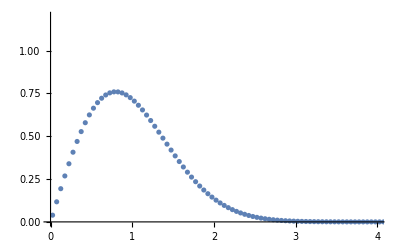

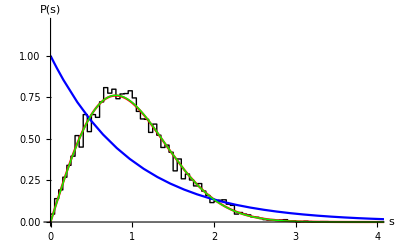

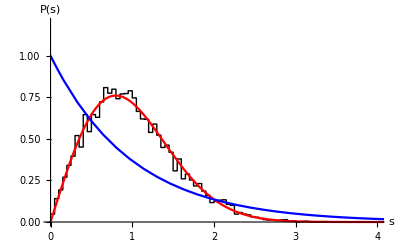

```mathematica
(*Normalisation*)
Clear[Norma];
Norma=Sum[(bin) Nhist[j],{j,1,Nofbins}];
Do[Nhist[j]=Nhist[j]/Norma,{j,1,Nofbins}];

Clear[jj,histEven,PlotEven];
jj=0;
histEven={};
Do[
jj+=1;
histEven=Append[histEven,{SPChist[jj],Nhist[jj]}];
histEven=Append[histEven,{SPChist[jj+1],Nhist[jj]}],
{j,1,Nofbins-1}]

PlotEven=
ListPlot[histEven,Joined-> True,PlotRange-> {{0,8},{0,1.2}},PlotStyle-> {Black,Thick},
LabelStyle-> Directive[Black,Bold,Medium],AxesLabel-> {"s","P(s)"}];
(*Tabling Distribution 'points' (x,y)*)

DistTable = Table[{(SPChist[j]+SPChist[j+1])/2,Nhist[j]},{j,1,Nofbins}];
(*Finding best fit for brody distribution*)
Bparam=FindFit[DistTable,(β+1)(Gamma[(β+2)/(β+1)])^(β+1) s^β E^(-(Gamma[(β+2)/(β+1)])^(β+1)  s^(β+1)),β,s]
Brody=
Plot[(β+1)(Gamma[(β+2)/(β+1)])^(β+1) s^β E^(-(Gamma[(β+2)/(β+1)])^(β+1)  s^(β+1))/.Bparam,{s,0,8},PlotRange->{0,1.2},PlotStyle->{Green,Thick},LabelStyle-> Directive[Black,Bold,Medium],AxesLabel-> {"s","P(s)"}];

(*Getting the κ parameter from pg 33 of the santos paper, first get list of spacing points, then evaluate WD at those points*)
spoints=Table[(SPChist[j]+SPChist[j+1])/2,{j,1,Nofbins}];
WDathistbars=Table[1/2 ⅇ^(-(π (s)^2)/4) π (s),{s,spoints}];
WDdist=Table[{spoints[[j]],WDathistbars[[j]]},{j,1,Nofbins}];

(*κ done here*)
κdenom = Sum[WDathistbars[[j]](bin),{j,1,Nofbins}]
distprob=Sum[Nhist[j](bin),{j,1,Nofbins}]
κ=1/κdenom √Sum[(bin(Nhist[j]-WDathistbars[[j]]))^2,{j,1,Nofbins}]
(*0.018 for WD*)

WignerDyson=
Plot[Pi s/2.Exp[-Pi s^2/4.],{s,0,8},PlotRange->{0,1.2},PlotStyle->{Red},LabelStyle-> Directive[White,Bold,Medium],AxesLabel-> {"s","P(s)"}];
Poisson=Plot[Exp[-s],{s,0,8},PlotRange-> {0,1.2},PlotStyle-> {Blue},LabelStyle-> Directive[White,Bold,Medium],AxesLabel-> {"s","P(s)"},PlotLabel->{"Poisson"}];

Show[{ListPlot[WDdist]},PlotRange-> {{0,4},{0,1.2}}]
Show[{PlotEven,WignerDyson,Poisson,Brody},PlotRange-> {{0,4},{0,1.2}}]
Show[{PlotEven,WignerDyson,Poisson},PlotRange-> {{0,4},{0,1.2}}]
UnitConvert[Quantity[AbsoluteTime[]-x,"Seconds"],MixedUnit[{"Minutes","Seconds"}]]
```

```mathematica
(*33min 28 seconds*)
```

33 28.634671